```mathematica
(*Simulation of scattering rate vs 866 satuation parameter*)
```

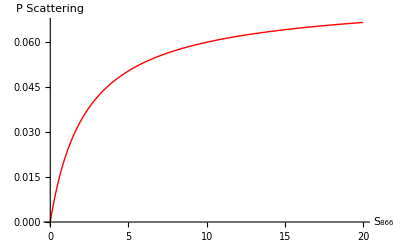

```mathematica
s1 = 0.8(*saturation parameter 397*);H=({{Subscript[Δ, g], Subscript[Ω, 12]/2, 0}, {Subscript[Ω, 12]/2, 0, Subscript[Ω, 23]/2}, {0, Subscript[Ω, 23]/2, Subscript[Δ, r]}});H0=H/.{Subscript[Δ, g]->-20,Subscript[Δ, r]->5,Subscript[Ω, 12]->√s1*22*0.93/√2,Subscript[Ω, 23]->√s2*22*0.07/√2};Subscript[C, 1]=√(22*0.93)({{0, 1, 0}, {0, 0, 0}, {0, 0, 0}}); (*P-S decay*)
Subscript[C, 2]=√(22*0.07)({{0, 0, 0}, {0, 0, 0}, {0, 1, 0}});(*P-D decay*)

Do[Subscript[CC, m]=(Subscript[C, m])†.Subscript[C, m],{m,2}];scanredintensity[s_]:=Module[{r,H=H0/.{s2->s},ρ},

ρ=Table[Subscript[r, {i,j}],{i,3},{j,3}];
r=ρ/.NSolve[ {ⅈ(H.ρ-ρ.H)==-1/2∑_(m=1)^2 (Subscript[CC, m]. ρ+ ρ.Subscript[CC, m] -2 Subscript[C, m] .ρ.(Subscript[C, m])†),Total[Diagonal[ρ]]==1},Flatten[ρ]]⟦1⟧;
Re@Diagonal@r
];data=Table[{s,scanredintensity[s]},{s,0,20,0.1}];
ListLinePlot[{{data⟦All,1⟧,data⟦All,2,2⟧}ᵀ},PlotRange->Full,PlotStyle->Directive[Red,Thick],AxesLabel->{"S_866","P Scattering"}]
```

```mathematica
24/23/(39/8)
```

64/299

```mathematica
N[64/299]
```

0.214047